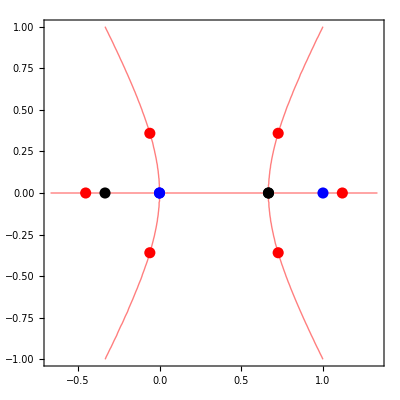

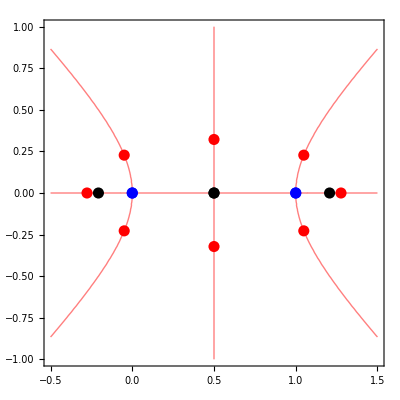

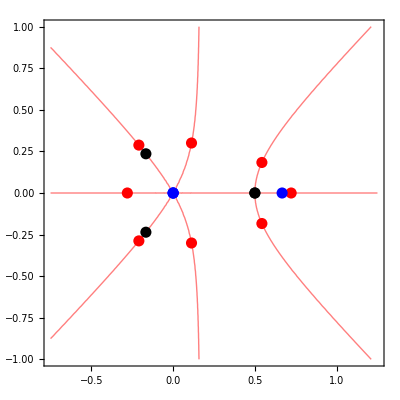

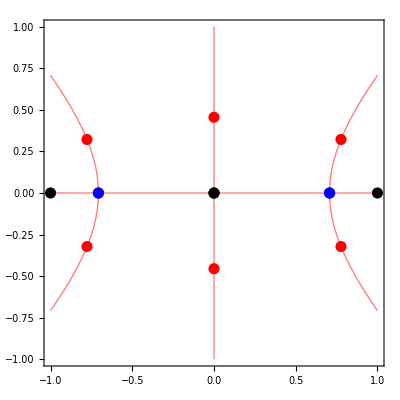

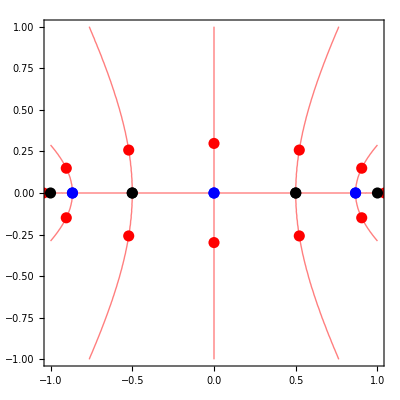

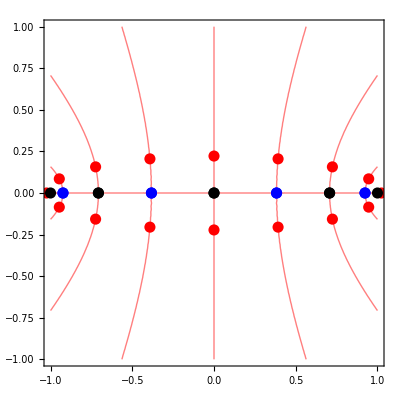

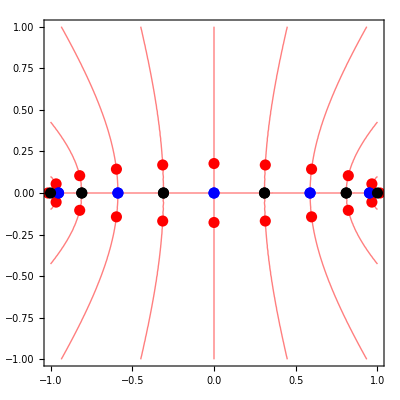

```mathematica
diag=1+I;
size=PointSize[0.02];
cheb[n_]:=ChebyshevT[n,z]^2;
proc[f_,a_,b_]:=Module[{p0,p1,p2,p3,p4,sol},
sol[t_]:=z/.Solve[f==t];
p0=ComplexContourPlot[Im[f],{z,a-b*diag,a+b*diag},
Contours->{0},ContourStyle->Red,ContourShading->False];
p1=ComplexListPlot[sol[-1],PlotStyle->{Red,size}];
p2=ComplexListPlot[sol[0],PlotStyle->{Blue,size}];
p3=ComplexListPlot[sol[1],PlotStyle->{Black,size}];
p4=ComplexListPlot[sol[2],PlotStyle->{Red,size}];
Show[p0,p1,p4,p2,p3]];
g1=27/4*z^2*(1-z);
g2=16*z^2*(1-z)^2;
h=16*z^3(2-3z);
proc[g1,1/3,1]
proc[g2,1/2,1]
proc[h,1/4,1]
proc[cheb[2],0,1]
proc[cheb[3],0,1]
proc[cheb[4],0,1]
proc[cheb[5],0,1]
```